```mathematica
basedir="D:\\";
files=FileNames["*.txt",basedir,5];
```

```mathematica
(*import data from all files without selecting further criteria*)
finalfiles=Table[
FileNameJoin[files[[i]]],
{i,1,Length[files]}];
finalfiles//TableForm;
rawdata=ReadList[#,String]&/@finalfiles;
```

```mathematica
(*specify which files to select based on some selection criteria; may or may not be necessary dependong on what you want to select*)
type="SeeMS";
splitfiles=Table[
FileNameSplit[files[[i]]],
{i,1,Length[files]}];
selectfiles=Cases[splitfiles,_?(StringContainsQ[#[[-2]],"SeeMS"]==True&)];
finalfiles=Table[
FileNameJoin[selectfiles[[i]]],
{i,1,Length[selectfiles]}];
finalfiles//TableForm;
rawdata=ReadList[#,String]&/@finalfiles;
```

```mathematica
splitpositions=
Table[
Flatten[
Position[
rawdata[[i]],s_String/;StringMatchQ[s,"*id: scan=*"]
]
]
,{i,Length[rawdata]}];
rawdatasplit=
Table[
SequenceSplit[rawdata[[i]],{_?(StringMatchQ[#,"*id: scan=*"]&)}]
,{i,Length[rawdata]}];
```

```mathematica
mzstart=
Table[
Position[rawdatasplit[[i,j]],s_String/;StringMatchQ[s,"*cvParam: m/z*"]][[1,1]]
,{i,Length[rawdatasplit]},{j,2,Length[rawdatasplit[[i]]]}];
mzdata=
Table[
ToExpression[
StringSplit[rawdatasplit[[i,j,mzstart[[i,j-1]]+1]]][[6;;-1]]
]
,{i,Length[rawdatasplit]},{j,2,Length[rawdatasplit[[i]]]}];
intstart=Table[
Position[rawdatasplit[[i,j]],s_String/;StringMatchQ[s,"*cvParam: intensity array*"]][[1,1]]
,{i,Length[rawdatasplit]},{j,2,Length[rawdatasplit[[i]]]}];
intdata=
Table[
ToExpression[
StringSplit[rawdatasplit[[i,j,intstart[[i,j-1]]+1]]][[6;;-1]]
]
,{i,Length[rawdatasplit]},{j,2,Length[rawdatasplit[[i]]]}];
```

```mathematica
rawspectra=
Table[
Transpose[{mzdata[[i,j]],intdata[[i,j]]}]
,
{i,Length[mzdata]},{j,Length[mzdata[[i]]]}];
avgint=
Table[
Mean[intdata[[i]]]
,
{i,Length[intdata]}];
avgspectra=
Table[
Transpose[{mzdata[[i,1]],avgint[[i]]}]
,
{i,Length[mzdata]}];
```

```mathematica
bckgndlvl=
Table[
Min[avgint[[i]]]
,
{i,Length[avgint]}];
bckgndsubint=
Table[
avgint[[i]]-bckgndlvl[[i]]
,
{i,Length[avgint]}];
bckgndsubspectra=Table[
Transpose[{mzdata[[i,1]],bckgndsubint[[i]]}]
,
{i,Length[mzdata]}];
```

```mathematica
maxint=
Table[
Max[bckgndsubint[[i]]]
,
{i,Length[bckgndsubint]}];
relint=
Table[
(bckgndsubint[[i]]/maxint[[i]])*100
,
{i,Length[bckgndsubint]}];
relintspectra=
Table[
Transpose[{mzdata[[i,1]],relint[[i]]}]
,
{i,Length[mzdata]}];
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
getMaxPadding[p_List]:=Map[Max,(BorderDimensions@Image[Show[#,LabelStyle->White,Background->White]]&/@p)~Flatten~{{3},{2}},{2}]+1
```

```mathematica
Table[{i,Part[FileNameSplit/@finalfiles,i,-1]},{i,Length[finalfiles]}]//TableForm
```

1 | MS_N3_P54_Dip_Phosser_10_10_1_MS_Negative_Dinj_028.txt
2 | MS_N3_P54_Dip_Phosser_10_10_2_MS_Negative_Dinj_030.txt
3 | MS_N3_P54_Dip_Phosser_10_10_3_MS_Negative_Dinj_032.txt
4 | MS_N3_P54_Dip_Phosser_20_10_1_MS_Negative_Dinj_022.txt
5 | MS_N3_P54_Dip_Phosser_20_10_2_MS_Negative_Dinj_024.txt
6 | MS_N3_P54_Dip_Phosser_20_10_3_MS_Negative_Dinj_026.txt
7 | MS_N3_P54_Dip_Phosser_30_10_1 001_MS_Negative_Dinj_016.txt
8 | MS_N3_P54_Dip_Phosser_30_10_2_MS_Negative_Dinj_018.txt
9 | MS_N3_P54_Dip_Phosser_30_10_3_MS_Negative_Dinj_020.txt
10 | MS_N3_P54_Dip_Phostyr_10_10_1_MS_Negative_Dinj_046.txt
11 | MS_N3_P54_Dip_Phostyr_10_10_2_MS_Negative_Dinj_048.txt
12 | MS_N3_P54_Dip_Phostyr_10_10_3_MS_Negative_Dinj_050.txt
13 | MS_N3_P54_Dip_Phostyr_20_10_1_MS_Negative_Dinj_040.txt
14 | MS_N3_P54_Dip_Phostyr_20_10_2_MS_Negative_Dinj_042.txt
15 | MS_N3_P54_Dip_Phostyr_20_10_3_MS_Negative_Dinj_044.txt
16 | MS_N3_P54_Dip_Phostyr_30_10_1_MS_Negative_Dinj_034.txt
17 | MS_N3_P54_Dip_Phostyr_30_10_2_MS_Negative_Dinj_036.txt
18 | MS_N3_P54_Dip_Phostyr_30_10_3_MS_Negative_Dinj_038.txt
19 | MS_N3_P54_Dip_STD_30uM_MS_Negative_Dinj_008.txt
20 | MS_N3_P54_PBP_Phosser_10_10_1_MS_Negative_Dinj_064.txt
21 | MS_N3_P54_PBP_Phosser_10_10_2_MS_Negative_Dinj_066.txt
22 | MS_N3_P54_PBP_Phosser_10_10_3_MS_Negative_Dinj_068.txt
23 | MS_N3_P54_PBP_Phosser_20_10_1_MS_Negative_Dinj_058.txt
24 | MS_N3_P54_PBP_Phosser_20_10_2_MS_Negative_Dinj_060.txt
25 | MS_N3_P54_PBP_Phosser_20_10_3_MS_Negative_Dinj_062.txt
26 | MS_N3_P54_PBP_Phosser_30_10_1_MS_Negative_Dinj_052.txt
27 | MS_N3_P54_PBP_Phosser_30_10_2_MS_Negative_Dinj_054.txt
28 | MS_N3_P54_PBP_Phosser_30_10_3_MS_Negative_Dinj_056.txt
29 | MS_N3_P54_PBP_Phostyr_10_10_1_MS_Negative_Dinj_082.txt
30 | MS_N3_P54_PBP_Phostyr_10_10_2_MS_Negative_Dinj_084.txt
31 | MS_N3_P54_PBP_Phostyr_10_10_3_MS_Negative_Dinj_086.txt
32 | MS_N3_P54_PBP_Phostyr_20_10_1_MS_Negative_Dinj_076.txt
33 | MS_N3_P54_PBP_Phostyr_20_10_2_MS_Negative_Dinj_078.txt
34 | MS_N3_P54_PBP_Phostyr_20_10_3_MS_Negative_Dinj_080.txt
35 | MS_N3_P54_PBP_Phostyr_30_10_1_MS_Negative_Dinj_070.txt
36 | MS_N3_P54_PBP_Phostyr_30_10_2_MS_Negative_Dinj_072.txt
37 | MS_N3_P54_PBP_Phostyr_30_10_3_MS_Negative_Dinj_074.txt
38 | MS_N3_P54_PBP_STD_30uM_MS_Negative_Dinj_010.txt
39 | MS_N3_P54_Phosser_STD_30uM_MS_Negative_Dinj_012.txt
40 | MS_N3_P54_Phostyr_STD_30uM_MS_Negative_Dinj_014.txt

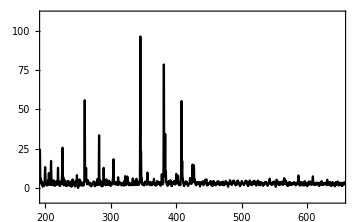
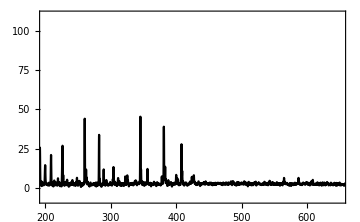
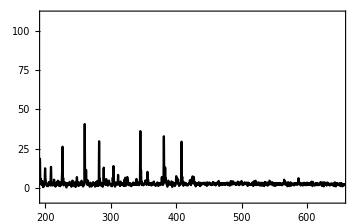
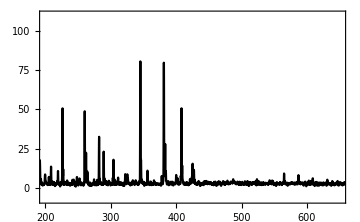
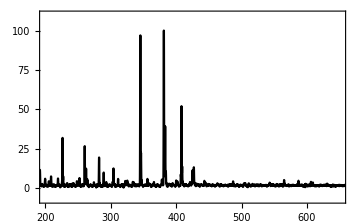
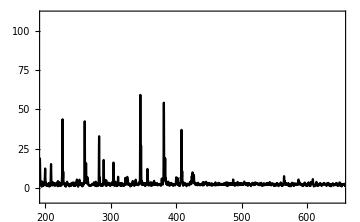
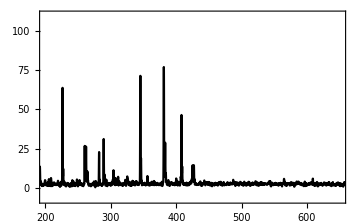
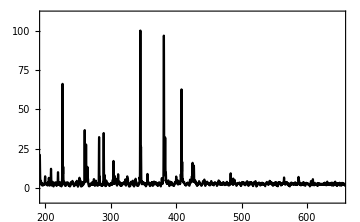
MS_N3_P54_PBP_Phostyr_10_10_1_MS_Negative_Dinj_082.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_10_10_2_MS_Negative_Dinj_084.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_10_10_3_MS_Negative_Dinj_086.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_20_10_1_MS_Negative_Dinj_076.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_20_10_2_MS_Negative_Dinj_078.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_20_10_3_MS_Negative_Dinj_080.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_30_10_1_MS_Negative_Dinj_070.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_30_10_2_MS_Negative_Dinj_072.txt
-Graphics-
MS_N3_P54_PBP_Phostyr_30_10_3_MS_Negative_Dinj_074.txt
-Graphics-

```mathematica
plotselectmod=Range[29,37,1];
specplotmod=
Table[{ListLinePlot[relintspectra[[i]],PlotStyle->Directive[RGBColor[0.,0.,0.]],PlotRange->{{ranges,rangee},{0-0.07*stackmax[[i]]*zoom[[i]]/100*zoomall/100,(stackmax[[i]]+0.1*stackmax[[i]])*zoom[[i]]/100*zoomall/100}},BaseStyle->{FontFamily->"Arial",FontSize->11},Frame->True,FrameStyle->Directive[Black,Thick],FrameLabel->Automatic,
LabelStyle->Black,
FrameTicks->{{If[yticks===False,
Table[If[EvenQ[Round[j/(stackmax[[i]]*zoom[[i]]/100*zoomall/100)*10]],{j,"",{0.01,0}},{j,"",{0.005,0}}],{j,0,stackmax[[i]]*zoom[[i]]/100*zoomall/100,stackmax[[i]]/10*zoom[[i]]/100*zoomall/100}]
,
Automatic]
,None},
{Automatic,
If[autogrid===False,
gridlines,
None]
	}},
FrameTicksStyle->Thick,
GridLines-> {gridlines,None},GridLinesStyle->Directive[Dashed,Thick]
,
ImageSize->Medium]}
,
{i,plotselectmod}
];
filelist=Table[Part[FileNameSplit/@finalfiles,i,-1],{i,Length[finalfiles]}];
Riffle[filelist[[plotselectmod]],specplotmod]//TableForm
```

```mathematica
plotselect={9,49,17};
xsize=230;
ysize=305;
ranges=50;
rangee=650;
stackmax=Table[100,{i,Length[relintspectra]}];
yticks=True;
zoomall=100;
zoom=Table[100,{i,Length[relintspectra]}];
autogrid=False;
gridlines=None;
specplot=
Table[{ListLinePlot[relintspectra[[i]],PlotStyle->Directive[RGBColor[0.,0.,0.]],PlotRange->{{ranges,rangee},{0-0.07*stackmax[[i]]*zoom[[i]]/100*zoomall/100,(stackmax[[i]]+0.1*stackmax[[i]])*zoom[[i]]/100*zoomall/100}},BaseStyle->{FontFamily->"Segoe UI",FontSize->10},Frame->True,FrameStyle->Directive[Black,Thickness[0.008]],FrameLabel->{None,None},
LabelStyle->Black,
FrameTicks->{{If[yticks===False,
Table[If[EvenQ[Round[j/(stackmax[[i]]*zoom[[i]]/100*zoomall/100)*10]],{j,"",{0.01,0}},{j,"",{0.005,0}}],{j,0,stackmax[[i]]*zoom[[i]]/100*zoomall/100,stackmax[[i]]/10*zoom[[i]]/100*zoomall/100}]
,
Automatic]
,None},
{Automatic,
If[autogrid===False,
gridlines,
None]
	}},
FrameTicksStyle->Directive[Black,Thickness[0.008]],
GridLines-> {gridlines,None},GridLinesStyle->Directive[Dashed],ImagePadding->{{1,1},{1,1}}]}
,
{i,plotselect}
];
Labeled[plotGrid[specplot,xsize,ysize,ImagePadding->20],
{Style["Relative Intensity",FontFamily->"Segoe UI",FontSize->10],Style["m/z",FontFamily->"Segoe UI",FontSize->10,Italic]},{Left,Bottom},RotateLabel->True]
```